```mathematica
dados = Import["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/FC - Projetos/P2/2a/RK_generico_2a.txt", "Table"]
```

{{0.01,0.999925,0,0,-0.0149246,0,0},{0.02,0.999702,0,0,-0.0296971,0,0},{0.03,0.999332,0,0,-0.0443154,0,0},{0.04,0.998816,0,0,-0.0587777,0,0},9993,{99.98,-0.919191,0,0,-0.271332,0,0},{99.99,-0.92186,0,0,-0.262513,0,0},{100,-0.924441,0,0,-0.253662,0,0}}
 |  |  |  |

```mathematica
posicao = dados[[All,{1,2}]]
```

{{0.01,0.999925},{0.02,0.999702},{0.03,0.999332},{0.04,0.998816},{0.05,0.998157},{0.06,0.997355},{0.07,0.996413},9986,{99.94,-0.907636},{99.95,-0.910656},{99.96,-0.913589},{99.97,-0.916434},{99.98,-0.919191},{99.99,-0.92186},{100,-0.924441}}
 |  |  |  |

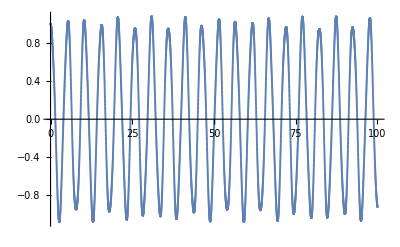

```mathematica
fig = ListPlot[posicao, PlotRange->All]
```